```mathematica
(* This function calculates QFIM of density matrix "mat" for variables "variables" *)
Fisher[mat_,variables_]:=(
result=Array[0&,{Length[variables],Length[variables]}];
evals=Simplify[Eigenvalues[mat]];
evecs=Simplify[Eigenvectors[mat]];
For[i=1,i≤Length[variables],i++,
For[j=1,j≤Length[variables],j++,
firstVar=variables[[i]];
secondVar=variables[[j]];
fisher1=fisher2=fisher3=0;
For[k=1,k≤Length[evals],k++,
If[evals[[k]]=!=0,
eval1=evals[[k]];
evec1=evecs[[k]];
KetEvec1=Simplify[Transpose[{evec1}]];
BraEvec1=Simplify[ConjugateTranspose[KetEvec1]];
norm1=Sqrt[(Simplify[BraEvec1.KetEvec1])[[1,1]]];
KetEvec1=Simplify[KetEvec1/norm1];
BraEvec1=Simplify[BraEvec1/norm1];
BraEvec1Prime1=D[BraEvec1,firstVar];
KetEvec1Prime1=D[KetEvec1,firstVar];
BraEvec1Prime2=D[BraEvec1,secondVar];
KetEvec1Prime2=D[KetEvec1,secondVar];

eval1Prime1=D[eval1,firstVar];
eval1Prime2=D[eval1,secondVar];

fisher1+=eval1Prime1*eval1Prime2/eval1;
fisher2+=eval1*Re[(BraEvec1Prime1.KetEvec1Prime2)[[1,1]]];
For[l=1,l≤Length[evals],l++,
If[evals[[l]]=!=0 ,
eval2=evals[[l]];
evec2=evecs[[l]];
KetEvec2=Simplify[Transpose[{evec2}]];
BraEvec2=Simplify[ConjugateTranspose[KetEvec2]];
norm2=Sqrt[(Simplify[BraEvec2.KetEvec2])[[1,1]]];
KetEvec2=Simplify[KetEvec2/norm2];
BraEvec2=Simplify[BraEvec2/norm2];
BraEvec2Prime1=D[BraEvec2,firstVar];
KetEvec2Prime1=D[KetEvec2,firstVar];
BraEvec2Prime2=D[BraEvec2,secondVar];
KetEvec2Prime2=D[KetEvec2,secondVar];
fisher3+=eval1*eval2*Re[(BraEvec1Prime1.KetEvec2)[[1,1]] *(BraEvec2.KetEvec1Prime2 )[[1,1]]]/(eval1+eval2);
];
];
];
];
Print[variables[[i]],variables[[j]]," done"];
result[[i,j]]=(fisher1+4*fisher2-8*fisher3)//Simplify;
];
];
ClearAll[i,j,k,l,fisher1,fisher2,fisher3,KetEvec1,KetEvec1Prime1,KetEvec1Prime2,KetEvec2,KetEvec2Prime1,KetEvec2Prime2,BraEvec1,BraEvec1Prime1,BraEvec1Prime2,BraEvec2,BraEvec2Prime1,BraEvec2Prime2,evecs,evec1,evec2,evals,eval1,eval1Prime1,eval2,eval1Prime2,firstVar,secondVar];
Return[result];
);
```

```mathematica
(* One Photon in lower branch - there are 6 distinct states *)
(* set global assumptions *)
$Assumptions={T,γ,ϕ}∈Reals&&T>=0&&T<=1; 
(* Define transmission and reflection coefficients *)
t=T Exp[-I γ];
r=Sqrt[1-T^2];
(* ψ={|1x,1a>,|1x,1b>,|1y,1a>,|1y,1b>,|1x,1w>,|1y,1w>} *)
a1=Sqrt[1/8](Exp[-I ϕ]-t);
a2=Sqrt[1/8](Exp[-I ϕ]+t);
a3=Sqrt[1-T^2]/2;

ψ={{a1},{-I a2},{I a2},{a1},{- a3},{I a3}};
ψ//MatrixForm
ρ=ψ.ConjugateTranspose[ψ]//ComplexExpand//Simplify;
```

((ⅇ^(-ⅈ ϕ)-ⅇ^(-ⅈ γ) T)/(2 √2)
-(ⅈ (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T))/(2 √2)
(ⅈ (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T))/(2 √2)
(ⅇ^(-ⅈ ϕ)-ⅇ^(-ⅈ γ) T)/(2 √2)
-1/2 √(1-T^2)
1/2 ⅈ √(1-T^2))

```mathematica
(* Tracing over dissipated photons in path |w> *)
For[i=1,i≤4,i++,
For[j=5,j≤6,j++,
If[i=!=j,ρ[[i,j]]=ρ[[j,i]]=0];
];
];
ρ//MatrixForm
```

(1/8 (1+T^2-2 T Cos[γ-ϕ]) | -1/8 ⅈ (-1+T^2-2 ⅈ T Sin[γ-ϕ]) | 1/8 ⅈ (-1+T^2-2 ⅈ T Sin[γ-ϕ]) | 1/8 (1+T^2-2 T Cos[γ-ϕ]) | 0 | 0
1/8 ⅈ (-1+T^2+2 ⅈ T Sin[γ-ϕ]) | 1/8 (1+T^2+2 T Cos[γ-ϕ]) | 1/8 (-1-T^2-2 T Cos[γ-ϕ]) | 1/8 ⅈ (-1+T^2+2 ⅈ T Sin[γ-ϕ]) | 0 | 0
1/8 (-ⅈ (-1+T^2)+2 T Sin[γ-ϕ]) | 1/8 (-1-T^2-2 T Cos[γ-ϕ]) | 1/8 (1+T^2+2 T Cos[γ-ϕ]) | 1/8 (-ⅈ (-1+T^2)+2 T Sin[γ-ϕ]) | 0 | 0
1/8 (1+T^2-2 T Cos[γ-ϕ]) | -1/8 ⅈ (-1+T^2-2 ⅈ T Sin[γ-ϕ]) | 1/8 ⅈ (-1+T^2-2 ⅈ T Sin[γ-ϕ]) | 1/8 (1+T^2-2 T Cos[γ-ϕ]) | 0 | 0
0 | 0 | 0 | 0 | 1/4 (1-T^2) | -1/4 ⅈ (-1+T^2)
0 | 0 | 0 | 0 | 1/4 ⅈ (-1+T^2) | 1/4 (1-T^2))

```mathematica
(* Calculate Quantum Fisher Information Matrix *)
fisher=Fisher[ρ,{ϕ,γ,T}];
```

ϕϕ done

ϕγ done

ϕT done

γϕ done

γγ done

γT done

Tϕ done

Tγ done

TT done

```mathematica
(* Simplify eqautions obtained for QFIM *)
fisher=fisher//ComplexExpand//Simplify;
fisher//MatrixForm
```

((2 T^2)/(1+T^2) | -(2 T^2)/(1+T^2) | 0
-(2 T^2)/(1+T^2) | (2 T^2)/(1+T^2) | 0
0 | 0 | -2/(-1+T^2))

```mathematica
(* Calulate determinant of QFIM *)
Det[fisher]
```

0

```mathematica
(* Calculate variance and covariance for objects characteristics *)
reducedfisher={{fisher[[2,2]],fisher[[2,3]]},{fisher[[3,2]],fisher[[3,3]]}};cov=Inverse[reducedfisher//Simplify]//Simplify;
cov//MatrixForm
```

(1/2 (1+1/T^2) | 0
0 | 1/2 (1-T^2))

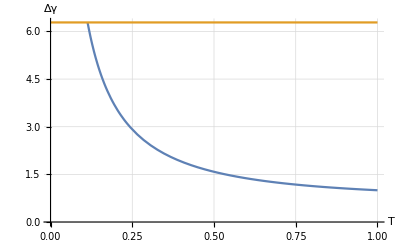

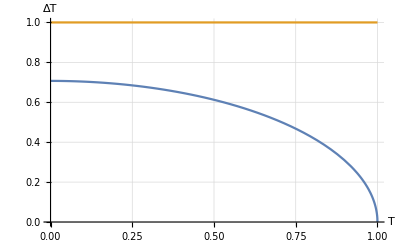

```mathematica
p1=Plot[{Sqrt[cov[[1,1]]],2*Pi},{T,0.001,1},PlotRange->{{0,1},{0,2Pi}},AxesLabel->{"T","Δγ"},GridLines->Automatic]
p2=Plot[{Sqrt[cov[[2,2]]],1},{T,0.001,1},PlotRange->{{0,1},{0,1}},AxesLabel->{"T","ΔT"},GridLines->Automatic]
Export["one-photon-dg.png",p1,ImageResolution->300];
Export["one-photon-dt.png",p2,ImageResolution->300];
```